b ⅇ^(a t)

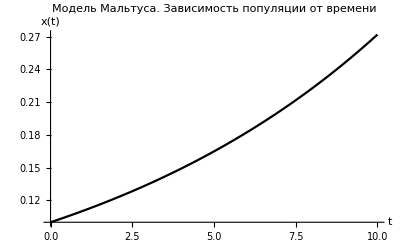

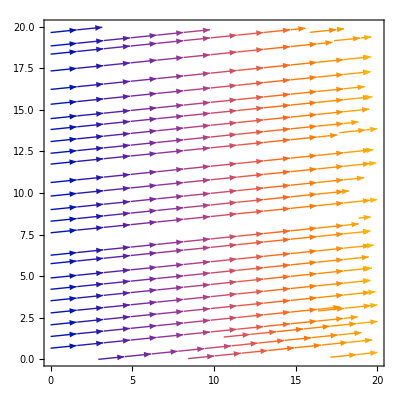

```mathematica
(*Модель Мальтуса*)
ClearAll["Global`*"];

Eq={x'[t]-a x[t]==0};
SolEq=DSolve[{Eq,x[0]==b},x[t],t][[1,1,2]]

Plot[{SolEq/. {a->0.1,b->0.1}},{t,0,10},PlotLabel->Style["Модель Мальтуса. Зависимость популяции от времени", 16],AxesLabel->{"t","x(t)"},PlotTheme->"Monochrome"]

Manipulate[Plot[b ⅇ^(a t),{t,0,10},PlotLabel->"Модель Мальтуса. Зависимость популяции от времени",AxesLabel->{"t","x(t)"},PlotTheme->"Monochrome"],{{a,0.1},0.5,1},{{b,0.1},0.5,3}]

StreamPlot[{x, 0.1x}, {x, 0, 20}, {y, 0, 20}]

Clear[Eq,SolEq]
```

DSolve::ifun: Inverse functions are being used by DSolve, so some solutions may not be found.

(b ⅇ^(a t))/(1-b+b ⅇ^(a t))

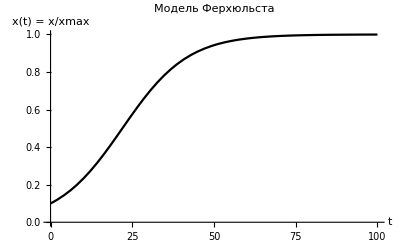

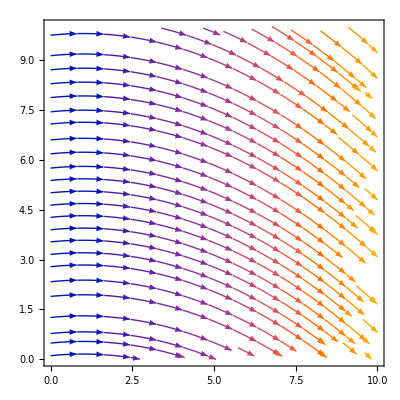

```mathematica
(*Модель Ферхюльста*)
ClearAll["Global`*"];

Eq = { x'[t] == a (1-x[t])x[t] };
SolEq = DSolve[{Eq, x[0] == b}, x[t], t][[1, 1, 2]]

Plot[SolEq /. {a -> 0.1, b -> 0.1}, {t, 0, 100}, PlotLabel->Style["Модель Ферхюльста", 16], AxesLabel->{"t", "x(t) = x/xmax"}, PlotTheme->"Monochrome"]

 Manipulate[Plot[(b ⅇ^(a t))/(1-b+b ⅇ^(a t)), {t, 0, 100}, PlotTheme->"Monochrome"], {a, -0.5, 0.5}, {b, 0.1, 2}]

StreamPlot[{x, 0.1(1-x)x},{x, 0, 10}, {y, 0, 10} ]

Clear[Eq,SolEq]
```

(b ⅇ^(a NN t) NN)/(-b-b c+b ⅇ^(a NN t)+b c ⅇ^(a NN t)+NN)

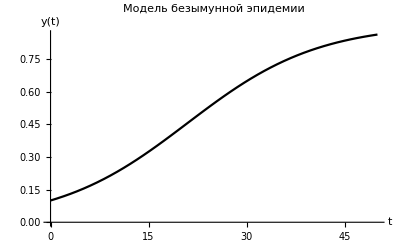

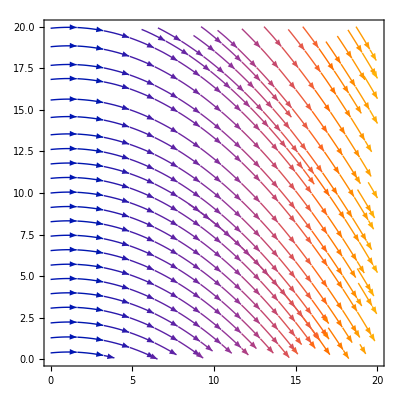

```mathematica
ClearAll["Global`*"];

Eq = { x'[t] == a x[t] (NN - x[t]-c x[t]) };
SolEq = DSolve[{Eq, x[0] == b}, x[t], t][[1,1,2]]

Plot[{SolEq /. {a -> 0.1, c->0.1, b -> 0.1, NN -> 1}}, {t, 0, 50}, PlotLabel->Style["Модель безымунной эпидемии", 16], AxesLabel->{"t", "y(t)"}, PlotTheme->"Monochrome"]

Manipulate[Plot[(b ⅇ^(a NN t) NN)/(-b-b c+b ⅇ^(a NN t)+b c ⅇ^(a NN t)+NN), {t, 0, 50}, PlotTheme->"Monochrome",PlotLabel->Style["Модель безымунной эпидемии", 16], AxesLabel->{"t", "y(t)"} ], {a, 0.1, 0.3}, {b, 0.1, 0.5}, {c, 0.1, 0.4}, {NN, 0.1, 2}]

StreamPlot[{x, 0.1x(1 - x(1 - 0.1))}, {x, 0, 20}, {y, 0, 20}]
```